# Testing one particular ttH@NNLO supergraph

## Resources

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"../../ltd_math_utils/LTDTools.m"
```

The documented functions in this package are: 
 ?plotGraph 
 ?findIsomorphicGraphs 
 ?constructCuts 
 ?importGraphs 
 ?getLoopLines 
 ?getCutStructure 
 ?writeMinimalJSON 
 ?extractTensCoeff 
 ?getSymCoeff 
 ?processNumerator 
 ?createSuperGraph 
 ?translateToFeynCalc
 ----------------------------------------- 
 Needs the package FeynCalc which can installed with Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"]; InstallFeynCalc[]
 Needs the package IGraphM which can be downloaded from https://github.com/szhorvat/IGraphM. !!! 
 Run: Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"] for installation.

FeynCalc 9.3.0 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

## Extracting the one ttH diagram of interest

```mathematica
(* First load all ttH  graphs *)
allTTHGraphs=importGraphs["./epem_ttH.qgr",sumIsoGraphs->False];
```

So we have many of them

```mathematica
Length[allTTHGraphs]
```

744

Many are however now the desired one, for instance:

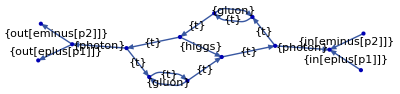

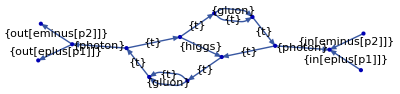

```mathematica
{plotGraph[allTTHGraphs⟦1⟧,edgeLabels->{"particleType"}],
plotGraph[allTTHGraphs⟦4⟧,edgeLabels->{"particleType"}]};
```

We can check if two diagrams are isomorphic simply with

```mathematica
findIsomorphicGraphs[allTTHGraphs⟦1;;4⟧,edgeTagging->{"particleType"}]
```

({3,2} | {}
{4,1} | {<|vertexMap→<|in(1)→in(1),v(1)→v(1),in(2)→in(2),out(1)→out(1),v(2)→v(2),out(2)→out(2),v(3)→v(3),v(4)→v(4),v(5)→v(5),v(6)→v(6),v(7)→v(7),v(8)→v(8),v(9)→v(9),v(10)→v(10)|>,permutation→Cycles[{}],orientationChange→{1,1,1,1,1,1,-1,-1,-1,-1,1,-1,1,-1,-1,1,-1}|>})

And we are only interested in one particular diagram which we will build here in order to find it in the list:

```mathematica
TargetDiagram=<|
"edges"->{
(* incoming photon *)
in[1]->v[1],in[2]->v[1],v[1]->v[3],
(* outgoing photon *)
v[4]->v[2],v[2]->out[1],v[2]->out[2],
(* top quark loop upper branch *)
v[3]->v[5],v[5]->v[6],v[6]->v[4],
(* top quark loop lower branch *)
v[4]->v[7],v[7]->v[8],v[8]->v[9],v[9]->v[10],v[10]->v[3],
(* gluons *)
v[5]->v[9],v[6]->v[8],
(* Higgs *)
v[10]->v[7]
},
"particleType"->{
in[eplus[p1]],in[eminus[p2]],photon,
photon,out[eplus[p1]],out[eminus[p2]],
t,t,t,
t,t,t,t,t,
gluon,gluon,
higgs
}
|>;
```

Now let’s find it in the list of diagrams

```mathematica
FindMyDiagram[diag_,OptionsPattern[{DEBUG->False}]]:=Block[
{diagIDsFound={}},
For[i=1,i≤Length[allTTHGraphs],++i,
If[OptionValue[DEBUG],Print["Now comparing with diag ID="<>ToString[i]];];
If[
findIsomorphicGraphs[{allTTHGraphs⟦i⟧,diag},edgeTagging->{"particleType"}]≠{},
AppendTo[diagIDsFound,i];
];
];
diagIDsFound
]
```

```mathematica
FindMyDiagram[TargetDiagram]
```

{65,72}

Check if these two diagrams are indeed the desired ones!

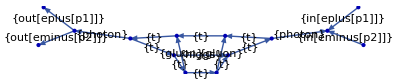

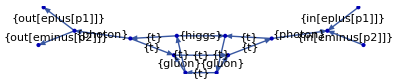

```mathematica
{plotGraph[allTTHGraphs⟦65⟧,edgeLabels->{"particleType"}],
plotGraph[allTTHGraphs⟦72⟧,edgeLabels->{"particleType"}]};
```

Yes they are!

```mathematica
SelectedDiagram=allTTHGraphs⟦65⟧;
```

## Processing that diagram

### Cutkosky cuts

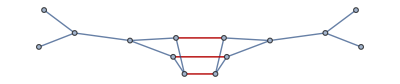

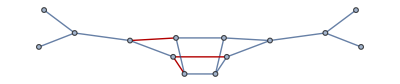

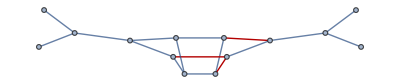

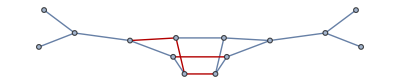

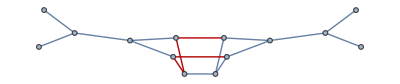

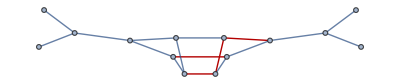

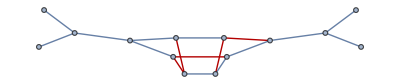

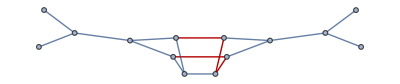

```mathematica
AllCutkoskyCutsOfSelectedDiagram=constructCuts[SelectedDiagram];
```

Below is a hard-coded filter to select only the 9 cutkosky cuts I am interested in

```mathematica
FilterCutkoskyCuts[allCuts_]:=Block[
{nTopCuts,nHiggsCuts,i,selectedCuts={},iCut,cutIndices},
For[i=1,i≤Length[allCuts],i++,
nTopCuts=0;
nHiggsCuts=0;
For[iCut=1,iCut≤Length[allCuts⟦i⟧["cutInfo"]],iCut++,
If[And[allCuts⟦i⟧["cutInfo"]⟦iCut⟧=="cut",allCuts⟦i⟧["particleType"]⟦iCut⟧==t],nTopCuts+=1;];
If[And[allCuts⟦i⟧["cutInfo"]⟦iCut⟧=="cut",allCuts⟦i⟧["particleType"]⟦iCut⟧==higgs],nHiggsCuts+=1;];
];
If[And[nTopCuts==2,nHiggsCuts==1],
AppendTo[selectedCuts,allCuts⟦i⟧];
];
];
selectedCuts
]
```

```mathematica
AllSelectedCutkoskyCutsOfSelectedDiagram=FilterCutkoskyCuts[AllCutkoskyCutsOfSelectedDiagram];
```

We should be left with 9 cuts.

```mathematica
Length[AllSelectedCutkoskyCutsOfSelectedDiagram]
```

9

Which are these:

```mathematica
Block[{graph,edges,i},
For[i=1,i≤Length[AllSelectedCutkoskyCutsOfSelectedDiagram],i++,
graph=AllSelectedCutkoskyCutsOfSelectedDiagram⟦i⟧;
edges=graph⟦"edges"⟧/. Rule[a_,b_]:>UndirectedEdge[a,b] /. DirectedEdge[a_,b_]:>UndirectedEdge[a,b]/. TwoWayRule[a_,b_]:>UndirectedEdge[a,b];
Print@HighlightGraph[edges,
Extract[edges,Position[graph["cutInfo"],"cut",Heads->False]]];
];
]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

We must now determine the basis in which to express our result for all 9 Cutkosky cut contributions

```mathematica
AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["momentumMap"]
```

{in(p1),in(p2),out(p1),out(p2),-p1-p2,p1+p2,-k1,-k1+p1+p2,k2,k2+p1+p2,-k3,k3-k1,k4,k1+k4-p1-p2,k2+k3,k2-k4+p1+p2,k3+k4-p1-p2}

```mathematica
AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["edges"]
```

{in(1)→v(1),in(2)→v(1),v(2)→out(1),v(2)→out(2),v(3)→v(1),v(4)→v(2),v(5)→v(3),v(3)→v(6),v(4)→v(7),v(8)→v(4),v(7)→v(5),v(9)→v(5),v(6)→v(8),v(9)→v(6),v(7)→v(10),v(10)→v(8),v(10)→v(9)}

```mathematica
AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["particleType"]
```

{in(eplus(p1)),in(eminus(p2)),out(eplus(p1)),out(eminus(p2)),photon,photon,t,t,t,t,higgs,t,t,gluon,t,gluon,t}

```mathematica
AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["cutInfo"]
```

{left,left,right,right,left,right,left,left,right,right,cut,left,cut,left,right,right,cut}

```mathematica
(AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["cutInfo"]⟦#⟧&)@{11,13,17}
(AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["particleType"]⟦#⟧&)@{11,13,17}
(AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["momentumMap"]⟦#⟧&)@{11,13,17}
(AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["edges"]⟦#⟧&)@{11,13,17}
```

{cut,cut,cut}

{higgs,t,t}

{-k3,k4,k3+k4-p1-p2}

{v(7)→v(5),v(6)→v(8),v(10)→v(9)}

```mathematica
FindCutEdgesIndices[cutDiagram_]:=Block[{iProp,cutIndices={}},
For[iProp=1,iProp≤Length[cutDiagram["cutInfo"]],iProp++,
If[cutDiagram["cutInfo"]⟦iProp⟧=="cut",
AppendTo[cutIndices,iProp];
];
];
cutIndices
]
```

```mathematica
BuildMomentumBasis[cutDiagram_]:=Block[{iProp,iCut,j,cutIndices,linearSystem={},finalLinearSystem={},
RemainingKs={k1,k2,k3,k4},
kis={k1,k2,k3,k4},
kisp={k1p,k2p,k3p,k4p}
},
cutIndices=FindCutEdgesIndices[cutDiagram];
For[iCut=1,iCut≤(Length[cutIndices]-1),iCut++,
AppendTo[linearSystem,Evaluate[kisp⟦iCut⟧]==cutDiagram["momentumMap"]⟦cutIndices⟦iCut⟧⟧];
For[j=1,j≤Length[kis],j++,
If[Coefficient[cutDiagram["momentumMap"]⟦cutIndices⟦iCut⟧⟧,kis⟦j⟧]≠0,
RemainingKs=DeleteCases[RemainingKs,kis⟦j⟧];
];
];
];
finalLinearSystem=linearSystem;
For[j=4,j>Length[linearSystem],j--,
AppendTo[finalLinearSystem,
Evaluate[kisp⟦4-j+Length[linearSystem]+1⟧]==Evaluate[RemainingKs⟦-(5-j)⟧]
];
];
Solve[finalLinearSystem,kis]⟦1⟧/.Table[
Evaluate[kisp⟦j⟧]->Evaluate[kis⟦j⟧]
,{j,Range[Length[kis]]}]
]
```

Generate all bases

```mathematica
AllSelectedCutkoskyCutsMomentumBases=Association[Table[
FindCutEdgesIndices[cutDiag]->BuildMomentumBasis[cutDiag],
{cutDiag,AllSelectedCutkoskyCutsOfSelectedDiagram}]]
```

<|{11,13,17}→{k1→k4,k2→k3,k3→-k1,k4→k2},{11,13,15,16}→{k1→k4,k2→k1+k3,k3→-k1,k4→k2},{11,12,13,14}→{k1→-k1-k2,k2→k4,k3→-k1,k4→k3},{10,11,16,17}→{k1→k4,k2→k1-p1-p2,k3→-k2,k4→k1-k3},{8,11,14,17}→{k1→-k1+p1+p2,k2→k4,k3→-k2,k4→k1+k3},{10,11,15}→{k1→k4,k2→k1-p1-p2,k3→-k2,k4→k3},{8,11,14,15,16}→{k1→-k1+p1+p2,k2→k2+k4,k3→-k2,k4→k1+k3},{8,11,12}→{k1→-k1+p1+p2,k2→k4,k3→-k2,k4→k3},{10,11,12,14,16}→{k1→-k2-k3,k2→k1-p1-p2,k3→-k2,k4→k2+k3+k4+p1+p2}|>

Generate the replacement rule to map the choice of basis in Rust (where each gluon carries an individual loop momentum)

```mathematica
FromQGrafToRustRotation=(Solve[
{
k1p==k1,
k2p==k1+k4-p1-p2,
k3p==-k3,
k4p==-k2+k4-p1-p2
}
,
{k1,k2,k3,k4}
]⟦1⟧)/.{k1p->k1,k2p->k2,k3p->k3,k4p->k4}
```

{k1→k1,k2→-k1+k2-k4,k3→-k3,k4→-k1+k2+p1+p2}

Combine two rotations

```mathematica
CombineRotations[rot1_,rot2_]:=Block[
{},
{
k1->Simplify[((k1/.rot1)/.rot2)],
k2->Simplify[((k2/.rot1)/.rot2)],
k3->Simplify[((k3/.rot1)/.rot2)],
k4->Simplify[((k4/.rot1)/.rot2)]
}
]
```

Therefore the combined rotations to apply for the generation of the polynomial for each CutKosky cut is:

```mathematica
FinalAllSelectedCutkoskyCutsMomentumBases=Association[Table[
key->CombineRotations[AllSelectedCutkoskyCutsMomentumBases[key],FromQGrafToRustRotation]
,{key,Keys[AllSelectedCutkoskyCutsMomentumBases]}]]
```

<|{11,13,17}→{k1→-k1+k2+p1+p2,k2→-k3,k3→-k1,k4→-k1+k2-k4},{11,13,15,16}→{k1→-k1+k2+p1+p2,k2→k1-k3,k3→-k1,k4→-k1+k2-k4},{11,12,13,14}→{k1→k4-k2,k2→-k1+k2+p1+p2,k3→-k1,k4→-k3},{10,11,16,17}→{k1→-k1+k2+p1+p2,k2→k1-p1-p2,k3→k1-k2+k4,k4→k1+k3},{8,11,14,17}→{k1→-k1+p1+p2,k2→-k1+k2+p1+p2,k3→k1-k2+k4,k4→k1-k3},{10,11,15}→{k1→-k1+k2+p1+p2,k2→k1-p1-p2,k3→k1-k2+k4,k4→-k3},{8,11,14,15,16}→{k1→-k1+p1+p2,k2→-2 k1+2 k2-k4+p1+p2,k3→k1-k2+k4,k4→k1-k3},{8,11,12}→{k1→-k1+p1+p2,k2→-k1+k2+p1+p2,k3→k1-k2+k4,k4→-k3},{10,11,12,14,16}→{k1→k1-k2+k3+k4,k2→k1-p1-p2,k3→k1-k2+k4,k4→-2 k1+2 k2-k3-k4+2 p1+2 p2}|>

### Further process the numerator:

```mathematica
(*SelectedDiagram["numerator"]*)
```

So we can now process the numerator:

```mathematica
Print["Now performing algebra of this diagram..."];
(*processedSelectedGraph=processNumerator[SelectedDiagram,"./minFeynRulesQCDH.m",spinSum->True,dimensions->4,additionalRules->{SP[p1,p1]->0,SP[p2,p2]->0,TF->1/2,ii->I,SP[k3,k3]->mH^2}];*)
processedSelectedGraph=Import["./processedSelectedGraphNew.m"];
Print["Done!"]
```

#### compare numerators

```mathematica
newNumerator=processedSelectedGraph[["numerator"]];
valsExpression=Import["./processedSelectedGraph.m"];
SP[x_List,y_List]/;NumericQ@x[[1]]:=x[[1]]*y[[1]]-x[[2;;]].y[[2;;]];
SP[x_List]:=x[[1]]*x[[1]]-x[[2;;]].x[[2;;]];
Table[
Print["numeric values"];
numRepl=Thread@Rule[Variables@valsExpression["momentumMap"],Table[RandomPrime[{5,500},4],{cc,Variables@valsExpression["momentumMap"]}]];
Print@numRepl;
valsNumerator=valsExpression[["numerator"]];
valsNumNumeric=valsNumerator/.Dispatch@numRepl;
newNumeratorNumeric=newNumerator/.Dispatch@numRepl;
Print["One evaluation: "<>ToString[(valsNumNumeric//Simplify),InputForm]];
Print["compare numerators: "<>ToString@(valsNumNumeric-newNumeratorNumeric//Simplify)];
Print["------------"];
,{tescount,10}];
```

#### Generate coefficients

```mathematica
MyPrefactor = ⅈ ge^4 gs^4 yt^2;
```

```mathematica
SelectedGraphNumeratorAsList=List@@processedSelectedGraph["numerator"];
```

```mathematica
ApplyFunctionToEachTerm[terms_,func_,OptionsPattern[{DEBUG->True,printoutFrequency->1,msgPrefix->""}]]:=Block[
{i, newTerms={},temp},
For[i=1,i≤Length[terms],i++,
If[And[OptionValue[DEBUG],Mod[i,OptionValue[printoutFrequency]]==0],
NotebookDelete[temp];
temp=PrintTemporary[OptionValue[msgPrefix]<>"Now processing terms >#"<>ToString[i]<>"..."]];
AppendTo[newTerms,func[terms⟦i⟧]];
];
NotebookDelete[temp];
newTerms
]
```

```mathematica
ProcessedSelectedGraphNumeratorAsList=ApplyFunctionToEachTerm[SelectedGraphNumeratorAsList,(Simplify[#/MyPrefactor])&,DEBUG->True,printoutFrequency->1000];
```

Now processing terms #1000...

Now processing terms #2000...

Now processing terms #3000...

Now processing terms #4000...

Now processing terms #5000...

Now processing terms #6000...

Now processing terms #7000...

Now processing terms #8000...

Now processing terms #9000...

Now processing terms #10000...

Now processing terms #11000...

Now processing terms #12000...

Now processing terms #13000...

Now processing terms #14000...

Now processing terms #15000...

Now processing terms #16000...

Now processing terms #17000...

Now processing terms #18000...

Now processing terms #19000...

Now processing terms #20000...

Now processing terms #21000...

Now processing terms #22000...

Now processing terms #23000...

Now processing terms #24000...

Now processing terms #25000...

Now processing terms #26000...

Now processing terms #27000...

Now processing terms #28000...

Now processing terms #29000...

Now processing terms #30000...

Now processing terms #31000...

Now processing terms #32000...

Now processing terms #33000...

Now processing terms #34000...

Now processing terms #35000...

Now processing terms #36000...

Now processing terms #37000...

Now processing terms #38000...

Quickly look at one coef:

```mathematica
ProcessedSelectedGraphNumeratorAsList⟦1⟧
```

(64 mH^2 mT^4 (OverBar[k1]·OverBar[p1]) (OverBar[k1]·OverBar[p2]))/Nc

```mathematica
MyEvaluateNumerator[numerator_,numRepl_]:=Block[{numericNum=numerator,Pair},
  numericNum=numericNum//FCI;
  Pair[Momentum[x_List,d___],Momentum[y_List,d___]]:=x[[1]]*y[[1]]-x[[2;;]].y[[2;;]];
  (* vectors are assumed to be covariant *)
   numericNum=(numerator//. numRepl //.x_List[y_Integer]:>If[y==0,x[[1]],-x[[y+1]] ]);
  If[Length@(Variables@numericNum)!=0,
  Print["Error: The numerator coefficients: "<>ToString[Variables@numericNum,InputForm]<>" have no numeric value!"];
  Abort[];  
  ];
  (* short vs long export format *)
  If[!ListQ[numericNum[[1]]],
    numericNum=((numericNum)/.x_/;NumericQ[x]:>ImportString[ExportString[(ReIm@x),"Real64"],"Real64"]),
    numericNum[[All,1]]=(numericNum[[All,1]]/.x_/;NumericQ[x]:>ImportString[ExportString[(ReIm@x),"Real64"],"Real64"]);    
  ];
  numericNum
];
```

```mathematica
BuildNumericalSymmetricCoeffs[analyticalExpression_,OptionsPattern[{consistencyCheckLevel->0,ReplacementRules->{}}]]:=Block[
{replRules={
p1->{1000.0,0,0,1000.0},
p2->{1000.0,0,0,-1000.0},
mH->125.0,mT->173.0,Nc->3, d->4
},
coeffs
},
coeffs=MyEvaluateNumerator[
getSymCoeff[<|
"numerator"->(ExpandScalarProduct[analyticalExpression/.OptionValue[ReplacementRules]]),
"momentumMap"->SelectedDiagram["momentumMap"],
"loopMomenta"->SelectedDiagram["loopMomenta"]
|>,outputFormat->"short",consistencyCheckLevel->OptionValue[consistencyCheckLevel]]["symmetrizedExpandedTensorCoeff"],
{
p1->{1000,0,0,1000},
p2->{1000,0,0,-1000},
mH->125,mT->173,Nc->3, d->4
}
];
(*coeffs*)
DeleteCases[coeffs,x_/;And[x⟦1⟧⟦1⟧==0,x⟦1⟧⟦2⟧==0]]
]
```

Test it!

```mathematica
getSymCoeff[<|
"numerator"->(ExpandScalarProduct[ProcessedSelectedGraphNumeratorAsList⟦1⟧/.{k1->k1+k2}]),
"momentumMap"->SelectedDiagram["momentumMap"],
"loopMomenta"->SelectedDiagram["loopMomenta"]
|>,outputFormat->"short",consistencyCheckLevel->0]["symmetrizedExpandedTensorCoeff"];
```

```mathematica
ExpandScalarProduct[ProcessedSelectedGraphNumeratorAsList⟦1⟧/.{k1->k1+k2}]
```

(64 mH^2 mT^4 (OverBar[k1]·OverBar[p1]+OverBar[k2]·OverBar[p1]) (OverBar[k1]·OverBar[p2]+OverBar[k2]·OverBar[p2]))/Nc

```mathematica
BuildNumericalSymmetricCoeffs[ProcessedSelectedGraphNumeratorAsList⟦1⟧,ReplacementRules->{k1->k1+k2}]
```

({2.98582×10^20,0.} | {0,0}
{5.97163×10^20,0.} | {0,4}
{-2.98582×10^20,0.} | {3,3}
{-5.97163×10^20,0.} | {3,7}
{2.98582×10^20,0.} | {4,4}
{-2.98582×10^20,0.} | {7,7})

```mathematica
SumCoeffs[coeffs_]:=Module[{SummedCoeffs,iCoeff,iCoeffsList, coeffPos},
SummedCoeffs={};
For[iCoeffsList=1,iCoeffsList≤Length[coeffs],iCoeffsList++,
For[iCoeff=1, iCoeff≤Length[coeffs⟦iCoeffsList⟧],iCoeff++,
coeffPos=FirstPosition[SummedCoeffs,{{_,_},coeffs⟦iCoeffsList⟧⟦iCoeff⟧⟦2⟧}];
If[coeffPos===Missing["NotFound"],
AppendTo[SummedCoeffs,coeffs⟦iCoeffsList⟧⟦iCoeff⟧];,
SummedCoeffs⟦coeffPos⟦1⟧⟧⟦1⟧⟦1⟧=SummedCoeffs⟦coeffPos⟦1⟧⟧⟦1⟧⟦1⟧+coeffs⟦iCoeffsList⟧⟦iCoeff⟧⟦1⟧⟦1⟧;
SummedCoeffs⟦coeffPos⟦1⟧⟧⟦1⟧⟦2⟧=SummedCoeffs⟦coeffPos⟦1⟧⟧⟦1⟧⟦2⟧+coeffs⟦iCoeffsList⟧⟦iCoeff⟧⟦1⟧⟦2⟧;
];
];
];
SummedCoeffs=DeleteCases[SummedCoeffs,x_/;And[x⟦1⟧⟦1⟧==0,x⟦1⟧⟦2⟧==0]];
SortBy[SummedCoeffs,(#⟦2⟧)&]
]
```

```mathematica
SumCoeffs[
{
BuildNumericalSymmetricCoeffs[ProcessedSelectedGraphNumeratorAsList⟦2⟧],
BuildNumericalSymmetricCoeffs[ProcessedSelectedGraphNumeratorAsList⟦1⟧]
}
]
```

({-1.19433×10^21,0.} | {0,0}
{1.19433×10^21,0.} | {3,3})

Example of summing the first two:

```mathematica
SumCoeffs[
{
BuildNumericalSymmetricCoeffs[ProcessedSelectedGraphNumeratorAsList⟦1⟧],
BuildNumericalSymmetricCoeffs[ProcessedSelectedGraphNumeratorAsList⟦2⟧]
}
]
```

({-1.19433×10^21,0.} | {0,0}
{1.19433×10^21,0.} | {3,3})

Build all coefficients

```mathematica
GenerateNumeratorCoefficients[numeratorAsListOfTerms_,OptionsPattern[{
consistencyCheckLevel->0,ReplacementRules->{},DEBUG->True,printoutFrequency->10000,msgPrefix->""
}]
]:=Block[
{overallCoeffs={},functionToApply},
functionToApply[x_]:=overallCoeffs=SumCoeffs[{overallCoeffs,BuildNumericalSymmetricCoeffs[x,
ReplacementRules->OptionValue[ReplacementRules],consistencyCheckLevel->OptionValue[consistencyCheckLevel]
]}];
ApplyFunctionToEachTerm[numeratorAsListOfTerms,functionToApply,
DEBUG->OptionValue[DEBUG],printoutFrequency->OptionValue[printoutFrequency],msgPrefix->OptionValue[msgPrefix]
];
overallCoeffs
]
```

We will then be able to generate all our desired coefficients for all Cutksoky cuts as follows:

```mathematica
FinalAllCoefficients=<||>;
(* Select below the range of terms to consider *)
MinIndex=1;
MaxTermIndex=4;
(* Chosing -1 below will run over all *)
(*MaxTermIndex=-1;*)
Block[{iCutkosky,tmp},
For[iCutkosky=1,iCutkosky≤Length[FinalAllSelectedCutkoskyCutsMomentumBases],iCutkosky++,
NotebookDelete[tmp];
tmp=PrintTemporary["Now generating coefficients for cutkosky cut #"<>ToString[iCutkosky]<>" ..."];
AppendTo[FinalAllCoefficients,
Keys[FinalAllSelectedCutkoskyCutsMomentumBases]⟦iCutkosky⟧->GenerateNumeratorCoefficients[
ProcessedSelectedGraphNumeratorAsList⟦MinIndex;;MaxTermIndex⟧,
DEBUG->True,
msgPrefix->("Cut #"<>ToString[iCutkosky]<>" : "),
printoutFrequency->1,
ReplacementRules->FinalAllSelectedCutkoskyCutsMomentumBases⟦iCutkosky⟧,
consistencyCheckLevel->0
]
];
];
]
```